The file format for the file is a list of points with seven entries each. The entries contain the following:

1) {x, y}, the parameter values over which the loop was iterated

2) {M1, M2, M3, M0, Mtau, 
MQ, MNR, tanβ, v, vevS, 
Atop, Abtm, Atau, An11, An12,
 An13, AlambdaN, Yn11, Yn12, Yn13, 
 lambda, lambdaN, kappa, PhisPI, Phi2PI, 
 ksi, Alambda, Akappa}, the input parameters
 
3) {χN-mass(5),  χC-mass(2), H+-mass(2), ν-mass(4), snu-mass(8), 
H0-mass(6), slep-mass(6), sup-mass(2), sdn-mass(2), stp-mass(2), 
sbt-mass(2)}, the mass eigenvalues, each of these is a vector in itself with the dimension noted in parentheses.

4) {χNre(5x5), χNim(5x5), 
χC-Ure(2x2),  χCU-im(2x2), χCV-re(2x2), χCV-im(2x2),  
νre(4x4), νim(4x4), 
H0(6x6), 
snu(8x8), 
slepCre(6x6), slepCim(6x6), 
sdown-re(2x2), sdown-im(2x2), sup-re(2x2), sup-im(2x2), stop-re(2x2), stop-im(2x2), sbottom-re(2x2), sbottom-im(2x2),
H+-(2x2)}, the mixing matrices, each of these is a nxn matrix with the dimensions noted in parentheses

5) {contribution in %, absolute contribution, channel}, the contributing channels to omega

6) {omega, CDM candidate name, Xf}, self explanatory

7) {cross section in pb, input channel, output channel}, cross sections for selected channels

8) CDM nucleon magic (amp = micromegas Amplitude, cs=cross section [pb])
{{n-cdm SI amp, n-anti-cdm SI amp, n-cdm SD amp, n-anti-cdm SD amp}, 
  {p-cdm SI amp, p-anti-cdm SI amp, p-cdm SD amp, p-anti-cdm SD amp}, 
  {n-cdm SI cs, n-anti-cdm SI cs, n-cdm SD cs, n-anti-cdm SD cs}, 
  {p-cdm SI cs, p-anti-cdm SI cs, p-cdm SD cs, p-anti-cdm SD cs}}

Load the data.

```mathematica
file1=<<"/Users/ruppell/Math/temp/output.txt";
label1="Fig CP";
```

```mathematica
First@Dimensions@file1
```

5

```mathematica
file4=<<"/Users/ruppell/Math/temp/output-combined.txt";
label2="Fig no CP";
```

```mathematica
mslc[i_]:=Abs@file1[[1,3,7,i]];
msln[i_]:=Abs@file1[[1,3,5,i]];
ml[i_]:={melectron,mmuon,mtau}[[i]];
Mc[l_]:=Abs@file1[[1,3,2,l]];
Mn[l_]:=Abs@file1[[1,3,1,l]];
```

```mathematica
vecCV=file1[[1,4,5]]+I file1[[1,4,6]];
vecCU=file1[[1,4,3]]+I file1[[1,4,4]];
vecN=file1[[1,4,1]]+I file1[[1,4,2]];
vNeutral=file1[[1,4,10]];
vCharged=file1[[1,4,11]]+I file1[[1,4,12]];
```

Some notational helpers

```mathematica
Rln[j_,k_]:=ml[j]^2/Mn[k]^2;
Rsln[j_,k_]:=mslc[j]^2/Mn[k]^2;
Rlc[j_,k_]:=ml[j]^2/Mc[k]^2;
Rsnc[j_,k_]:=msln[j]^2/Mc[k]^2;
```

The loop integrals from the box diagram for k-kbar and the loop for the EDMs

```mathematica
vSign=1;(*Signs are:vSign=1=own=Moroi*-1, vSign=-1=Rosiek*)
σNe[i_]:=Sign[file1[[1,3,1,i]]];
σCh[i_]:=Sign[file1[[1,3,2,i]]];

cR[i_,j_,k_]:=-  g2 σCh[j]Conjugate[vecCV[[j,1]]]vNeutral[[k,i]]+hN[i]σCh[j]Conjugate[vecCV[[j,2]]]vNeutral[[k,i]];
cL[i_,j_,k_]:= hE[i,i]σCh[j]vecCU[[j,2]]vNeutral[[k,i]];
nR[i_,j_,k_]:=1/Sqrt[2](g1 Conjugate[vecN[[j,1]]]+g2 Conjugate[vecN[[j,2]]])σNe[j]vCharged[[k,i]]-Conjugate[hE[i,i]]σNe[j]Conjugate[vecN[[j,3]]]vCharged[[k,i+3]];
nL[i_,j_,k_]:=- Sqrt[2]g1 vecN[[j,1]]σNe[j]vCharged[[k,i+3]]-hE[i,i]σNe[j]vecN[[j,3]]vCharged[[k,i]];

method="bartl";(*Possible values bartl moroi hisano*)
If[method==="bartl",
Fx1[x_]:=-(2+3x-6x^2+x^3+6x Log[x])/(6(1-x)^4);
Fx2[x_]:=(1-6x+3x^2+2x^3-6x^2 Log[x])/(6(1-x)^4);
Fx3[x_]:=-(1-x^2+2x Log[x])/(1-x)^3;
Fx4[x_]:=(1-4x+3x^2-2x^2 Log[x])/(1-x)^3;

aLcχnl[i_,j_]:=1/(16 Pi^2)Table[(nL[i,k,r]Conjugate[nL[j,k,r]]Rln[j,k]+nR[i,k,r]Conjugate[nR[j,k,r]]Rln[i,k])Fx1[Rsln[r,k]]+
nL[i,k,r]Conjugate[nR[j,k,r]]Sqrt[Rln[j,k]]Fx3[Rsln[r,k]],{k,1,4},{r,1,6}];
aLnχcl[i_,j_]:=1/(16 Pi^2)
Table[(cL[i,k,r]Conjugate[cL[j,k,r]]Rlc[j,k]+cR[i,k,r]Conjugate[cR[j,k,r]]Rlc[i,k])Fx2[Rsnc[r,k]]+
cL[i,k,r]Conjugate[cR[j,k,r]]Sqrt[Rlc[j,k]]Fx4[Rsnc[r,k]],{k,1,2},{r,1,3}];
aRcχnl[i_,j_]:=1/(16 Pi^2)Table[(nR[i,k,r]Conjugate[nR[j,k,r]]Rln[j,k]+nL[i,k,r]Conjugate[nL[j,k,r]]Rln[i,k])Fx1[Rsln[r,k]]+
nR[i,k,r]Conjugate[nL[j,k,r]]Sqrt[Rln[j,k]]Fx3[Rsln[r,k]],{k,1,4},{r,1,6}];
aRnχcl[i_,j_]:=1/(16 Pi^2)
Table[(cR[i,k,r]Conjugate[cR[j,k,r]]Rlc[j,k]+cL[i,k,r]Conjugate[cL[j,k,r]]Rlc[i,k])Fx2[Rsnc[r,k]]+
cR[i,k,r]Conjugate[cL[j,k,r]]Sqrt[Rlc[j,k]]Fx4[Rsnc[r,k]],{k,1,2},{r,1,3}];

aL[i_,j_]:=1/(16 Pi^2)(Sum[(nL[i,k,r]Conjugate[nL[j,k,r]]Rln[j,k]+nR[i,k,r]Conjugate[nR[j,k,r]]Rln[i,k])Fx1[Rsln[r,k]]+
nL[i,k,r]Conjugate[nR[j,k,r]]Sqrt[Rln[j,k]]Fx3[Rsln[r,k]],{k,1,4},{r,1,6}]+
Sum[(cL[i,k,r]Conjugate[cL[j,k,r]]Rlc[j,k]+cR[i,k,r]Conjugate[cR[j,k,r]]Rlc[i,k])Fx2[Rsnc[r,k]]+
cL[i,k,r]Conjugate[cR[j,k,r]]Sqrt[Rlc[j,k]]Fx4[Rsnc[r,k]],{k,1,2},{r,1,3}]);
aR[i_,j_]:=1/(16 Pi^2)(Sum[(nR[i,k,r]Conjugate[nR[j,k,r]]Rln[j,k]+nL[i,k,r]Conjugate[nL[j,k,r]]Rln[i,k])Fx1[Rsln[r,k]]+
nR[i,k,r]Conjugate[nL[j,k,r]]Sqrt[Rln[j,k]]Fx3[Rsln[r,k]],{k,1,4},{r,1,6}]+
Sum[(cR[i,k,r]Conjugate[cR[j,k,r]]Rlc[j,k]+cL[i,k,r]Conjugate[cL[j,k,r]]Rlc[i,k])Fx2[Rsnc[r,k]]+
cR[i,k,r]Conjugate[cL[j,k,r]]Sqrt[Rlc[j,k]]Fx4[Rsnc[r,k]],{k,1,2},{r,1,3}]);

Δa[i_]:=1/2Re[aR[i,i]+aL[i,i]];
edm[i_]:=hc Sqrt[αew 4 Pi]1/(4 ml[i])Im[aR[i,i]-aL[i,i]];
Γllg[j_,i_]:=αew ml[j]/16(Abs[aL[i,j]]^2+Abs[aR[i,j]]^2);
BRllg[j_,i_]:=Which[j<=i,0,
j==2,192Pi^3/(GF^2 ml[j]^5)Γllg[j,i],
j==3,192Pi^3/(GF^2 ml[j]^5)Γllg[j,i]BRτνν];
];
```

```mathematica
mu[i_]:=Sqrt[Abs[{msQu[1][[1]],msQu[1][[2]],msQu[2][[1]],msQu[2][[2]],msQu[3][[1]],msQu[3][[2]]}]][[i]];
md[i_]:=Sqrt[Abs[{msQd[1][[1]],msQd[1][[2]],msQd[2][[1]],msQd[2][[2]],msQd[3][[1]],msQd[3][[2]]}]][[i]];
Mc[l_]:=Abs[Flatten[{mCharginos,mCharginos}]][[l]]
Mn[l_]:=Abs[mNeutrinos][[l]];
```

Some notational helpers

```mathematica
rmu[x_,i_]:=mu[x]^2/mu[i]^2;
rMc[x_,i_]:=Mc[x]^2/mu[i]^2;
Rmm[x_,y_,i_]:=rmu[x,i]-rmu[y,i];
RMM[x_,y_,i_]:=rMc[x,i]-rMc[y,i];
RMm[x_,y_,i_]:=rMc[x,i]-rmu[y,i];
RmM[x_,y_,i_]:=rmu[x,i]-rMc[y,i];
```

The loop integrals from the box diagram for k-kbar and the loop for the EDMs

```mathematica
Int1[i_,j_,k_,l_]:=Which[
(Mc[k]==0)||(Mc[l]==0),
0,
(mu[i]!=mu[j])&&(Mc[k]!=Mc[l]),
RMm[l,j,i]^-1*
(RmM[j,k,i]^-1*
(Rmm[j,i,i]^-1(1/2(1-Rmm[i,j,i])^2(Log[1-Rmm[i,j,i]]-1/2)+1/4)-
RMm[k,i,i]^-1(1/2(1-RmM[i,k,i])^2(Log[1-RmM[i,k,i]]-1/2)+1/4))-
RMM[l,k,i]^-1*
(RMm[l,i,i]^-1(1/2(1-RmM[i,l,i])^2(Log[1-RmM[i,l,i]]-1/2)+1/4)-
RMm[k,i,i]^-1(1/2(1-RmM[i,k,i])^2(Log[1-RmM[i,k,i]]-1/2)+1/4))),
(mu[i]==mu[j])&&(Mc[k]!=Mc[l]),
RMm[l,j,i]^-1*
(RmM[j,k,i]^-1*
(-RMm[k,i,i]^-1(1/2(1-RmM[i,k,i])^2(Log[1-RmM[i,k,i]]-1/2)+1/4))-
RMM[l,k,i]^-1*
(RMm[l,i,i]^-1(1/2(1-RmM[i,l,i])^2(Log[1-RmM[i,l,i]]-1/2)+1/4)-
RMm[k,i,i]^-1(1/2(1-RmM[i,k,i])^2(Log[1-RmM[i,k,i]]-1/2)+1/4))),
(mu[i]!=mu[j])&&(Mc[k]==Mc[l]),
RMm[l,j,i]^-1*
(RmM[j,k,i]^-1*
(Rmm[j,i,i]^-1(1/2(1-Rmm[i,j,i])^2(Log[1-Rmm[i,j,i]]-1/2)+1/4)-
RMm[k,i,i]^-1(1/2(1-RmM[i,k,i])^2(Log[1-RmM[i,k,i]]-1/2)+1/4))),
(mu[i]==mu[j])&&(Mc[k]==Mc[l]),
RMm[l,j,i]^-1*
(RmM[j,k,i]^-1*
(-RMm[k,i,i]^-1(1/2(1-RmM[i,k,i])^2(Log[1-RmM[i,k,i]]-1/2)+1/4)))];

Int2[i_,j_,k_,l_]:=Which[
(Mc[k]==0)||(Mc[l]==0),
0,
(mu[i]!=mu[j])&&(Mc[k]!=Mc[l]),
RmM[j,l,i]^-1*
(RMM[l,k,i]^-1*
(RMm[l,i,i]^-1(1-RmM[i,l,i])Log[1-RmM[i,l,i]]-1-
RMm[k,i,i]^-1(1-RmM[i,k,i])Log[1-RmM[i,k,i]]+1)-
RmM[j,k,i]^-1*
(Rmm[j,i,i]^-1(1-Rmm[i,j,i])Log[1-Rmm[i,j,i]]-1-
RMm[k,i,i]^-1(1-RmM[i,k,i])Log[1-RmM[i,k,i]]+1)),
(mu[i]==mu[j])&&(Mc[k]!=Mc[l]),
RmM[j,l,i]^-1*
(RMM[l,k,i]^-1*
(RMm[l,i,i]^-1(1-RmM[i,l,i])Log[1-RmM[i,l,i]]-1-
RMm[k,i,i]^-1(1-RmM[i,k,i])Log[1-RmM[i,k,i]]+1)-
RmM[j,k,i]^-1*
(-RMm[k,i,i]^-1(1-RmM[i,k,i])Log[1-RmM[i,k,i]]+1)),
(mu[i]!=mu[j])&&(Mc[k]==Mc[l]),
RmM[j,l,i]^-1*
(-RmM[j,k,i]^-1*
(Rmm[j,i,i]^-1(1-Rmm[i,j,i])Log[1-Rmm[i,j,i]]-1-
RMm[k,i,i]^-1(1-RmM[i,k,i])Log[1-RmM[i,k,i]]+1)),
(mu[i]==mu[j])&&(Mc[k]==Mc[l]),
RmM[j,l,i]^-1*
(-RmM[j,k,i]^-1*
(-RMm[k,i,i]^-1(1-RmM[i,k,i])Log[1-RmM[i,k,i]]+1))];

A[r_]:=1/(2(1-r)^2)(3-r+2 Log[r]/(1-r));
B[r_]:=1/(2(1-r)^2)(1+r+2r Log[r]/(1-r));
```

The "percentages" of gauge eigenstates in each mass eigenstate, i.e., the diagonalization matrices.

```mathematica
Pchχ[i_,j_]:={Flatten[{vCharginos[[1,1]],0,0,0,0,0}],
Flatten[{vCharginos[[1,2]],0,0,0,0,0}],
Flatten[{vCharginos[[1,3]],0,0,0,0,0}],
Flatten[{vCharginos[[1,4]],0,0,0,0,0}],
Flatten[{vCharginos[[1,5]],0,0,0,0,0}],
Flatten[{0,0,0,0,0,vCharginos[[2,1]]}],
Flatten[{0,0,0,0,0,vCharginos[[2,2]]}],
Flatten[{0,0,0,0,0,vCharginos[[2,3]]}],
Flatten[{0,0,0,0,0,vCharginos[[2,4]]}],
Flatten[{0,0,0,0,0,vCharginos[[2,5]]}]}[[i,j]];
PchχC[i_,j_]:=Conjugate[Pchχ[i,j]];
Pneχ[i_,j_]:=vNeutrinos[[i,j]];
PneχC[i_,j_]:=Conjugate[vNeutrinos[[i,j]]];
PsQu[i_,j_]:={Flatten[{vsQu[1][[1]],0,0,0,0}],
Flatten[{vsQu[1][[2]],0,0,0,0}],
Flatten[{0,0,vsQu[2][[1]],0,0}],
Flatten[{0,0,vsQu[2][[2]],0,0}],
Flatten[{0,0,0,0,vsQu[3][[1]]}],
Flatten[{0,0,0,0,vsQu[3][[2]]}]}[[i,j]];
PsQuC[i_,j_]:=Conjugate[PsQu[i,j]];
PsQd[i_,j_]:={Flatten[{vsQd[1][[1]],0,0,0,0}],
Flatten[{vsQd[1][[2]],0,0,0,0}],
Flatten[{0,0,vsQd[2][[1]],0,0}],
Flatten[{0,0,vsQd[2][[2]],0,0}],
Flatten[{0,0,0,0,vsQd[3][[1]]}],
Flatten[{0,0,0,0,vsQd[3][[2]]}]}[[i,j]];
PsQdC[i_,j_]:=Conjugate[PsQd[i,j]];
```

The names of the gauge fields, this is used later in for symbolic derivation of the vertex coefficients

```mathematica
Lchχ={λm,fHupC,ϵ[1],ϵ[2],ϵ[3],λpC,fHdm,e[1],e[2],e[3]};
LchχC={λp,fHdmC,eC[1],eC[2],eC[3],λmC,fHup,ϵC[1],ϵC[2],ϵC[3]};
Lneχ={ν[1],ν[2],ν[3],nC[1],fHd0,fHu0,λ0,λ3};
LneχC={νC[1],νC[2],νC[3],n[1],fHd0C,fHu0C,λ0C,λ3C};
LsQu={sυ[1],su[1],sυ[2],su[2],sυ[3],su[3]};
LsQd={sδ[1],sd[1],sδ[2],sd[2],sδ[3],sd[3]};
LsQuC={sυC[1],suC[1],sυC[2],suC[2],sυC[3],suC[3]};
LsQdC={sδC[1],sdC[1],sδC[2],sdC[2],sδC[3],sdC[3]};
```

The Vertex coefficients, defined by the outgoing quark leg. For chargino+squark and neutralino+squark. Note: making these explicit instead of SetDelayed speeds up the eventual calculation a lot.

```mathematica
Vcδ[1]=Outer[D[Vv,δ[1],#1,#2]&,LsQuC,LchχC];Vcδ[2]=Outer[D[Vv,δ[2],#1,#2]&,LsQuC,LchχC];
VcδC[1]=Outer[D[Vv,δC[1],#1,#2]&,LsQu,Lchχ];VcδC[2]=Outer[D[Vv,δC[2],#1,#2]&,LsQu,Lchχ];
VcdC[1]=Outer[D[Vv,dC[1],#1,#2]&,LsQu,Lchχ];VcdC[2]=Outer[D[Vv,dC[2],#1,#2]&,LsQu,Lchχ];
Vcd[1]=Outer[D[Vv,d[1],#1,#2]&,LsQuC,LchχC];Vcd[2]=Outer[D[Vv,d[2],#1,#2]&,LsQuC,LchχC];

Vnδ[1]=Outer[D[Vv,δ[1],#1,#2]&,LsQdC,Lneχ];
VnδC[1]=Outer[D[Vv,δC[1],#1,#2]&,LsQd,LneχC];
VndC[1]=Outer[D[Vv,dC[1],#1,#2]&,LsQd,Lneχ];
Vnd[1]=Outer[D[Vv,d[1],#1,#2]&,LsQdC,LneχC];

Vcυ[1]=Outer[D[Vv,υ[1],#1,#2]&,LsQdC,Lchχ];
VcυC[1]=Outer[D[Vv,υC[1],#1,#2]&,LsQd,LchχC];
VcuC[1]=Outer[D[Vv,uC[1],#1,#2]&,LsQd,LchχC];
Vcu[1]=Outer[D[Vv,u[1],#1,#2]&,LsQdC,Lchχ];

Vnυ[1]=Outer[D[Vv,υ[1],#1,#2]&,LsQuC,Lneχ];
VnυC[1]=Outer[D[Vv,υC[1],#1,#2]&,LsQu,LneχC];
VnuC[1]=Outer[D[Vv,uC[1],#1,#2]&,LsQu,Lneχ];
Vnu[1]=Outer[D[Vv,u[1],#1,#2]&,LsQuC,LneχC];
```

The vertices grouped by the outgoing quark leg and as functions of squark index (i) and chargino/neutralino index (j)

```mathematica
VLdchχ[f_,i_,j_]:=PsQuC[i,Range[1,6]].Vcδ[f].PchχC[j,Range[1,10]];
VLdchχC[f_,i_,j_]:=PsQu[i,Range[1,6]].VcδC[f].Pchχ[j,Range[1,10]];
VRdchχ[f_,i_,j_]:=PsQu[i,Range[1,6]].VcdC[f].Pchχ[j,Range[1,10]];
VRdchχC[f_,i_,j_]:=PsQuC[i,Range[1,6]].Vcd[f].PchχC[j,Range[1,10]];

VLuchχ[f_,i_,j_]:=PsQdC[i,Range[1,6]].Vcυ[f].Pchχ[j,Range[1,10]];
VLuchχC[f_,i_,j_]:=PsQd[i,Range[1,6]].VcυC[f].PchχC[j,Range[1,10]];
VRuchχ[f_,i_,j_]:=PsQd[i,Range[1,6]].VcuC[f].PchχC[j,Range[1,10]];
VRuchχC[f_,i_,j_]:=PsQdC[i,Range[1,6]].Vcu[f].Pchχ[j,Range[1,10]];

VLuneχ[f_,i_,j_]:=PsQuC[i,Range[1,6]].Vnυ[f].Pneχ[j,Range[1,8]];
VLuneχC[f_,i_,j_]:=PsQu[i,Range[1,6]].VnυC[f].PneχC[j,Range[1,8]];
VRuneχ[f_,i_,j_]:=PsQu[i,Range[1,6]].VnuC[f].Pneχ[j,Range[1,8]];
VRuneχC[f_,i_,j_]:=PsQuC[i,Range[1,6]].Vnu[f].PneχC[j,Range[1,8]];

VLdneχ[f_,i_,j_]:=PsQdC[i,Range[1,6]].Vnδ[f].Pneχ[j,Range[1,8]];
VLdneχC[f_,i_,j_]:=PsQd[i,Range[1,6]].VnδC[f].PneχC[j,Range[1,8]];
VRdneχ[f_,i_,j_]:=PsQd[i,Range[1,6]].VndC[f].Pneχ[j,Range[1,8]];
VRdneχC[f_,i_,j_]:=PsQdC[i,Range[1,6]].Vnd[f].PneχC[j,Range[1,8]];
```

The L-R combinatorics from the matrix element calculation

```mathematica
W1[i_,j_,k_,l_]:=VLdchχC[2,i,l]VLdchχ[1,j,l]VLdchχC[2,j,k]VLdchχ[1,i,k]+
                                       VRdchχC[2,i,l]VRdchχ[1,j,l]VRdchχC[2,j,k]VRdchχ[1,i,k];
W2[i_,j_,k_,l_]:=VLdchχC[2,i,l]VLdchχ[1,j,l]VRdchχC[2,j,k]VRdchχ[1,i,k]+
                                       VRdchχC[2,i,l]VRdchχ[1,j,l]VLdchχC[2,j,k]VLdchχ[1,i,k];
W3[i_,j_,k_,l_]:=VLdchχC[2,i,l]VRdchχ[1,j,l]VLdchχC[2,j,k]VRdchχ[1,i,k]+
                                       VRdchχC[2,i,l]VLdchχ[1,j,l]VRdchχC[2,j,k]VLdchχ[1,i,k];
W4[i_,j_,k_,l_]:=VLdchχC[2,i,l]VRdchχ[1,j,l]VRdchχC[2,j,k]VLdchχ[1,i,k]+
                                       VRdchχC[2,i,l]VLdchχ[1,j,l]VLdchχC[2,j,k]VRdchχ[1,i,k];

ImKLucχ[i_,k_]:=Im[VLuchχ[1,k,i]VRuchχC[1,k,i]];
ImKLunχ[i_,k_]:=Im[VLuneχ[1,k,i]VRuneχC[1,k,i]];
ImKLdcχ[i_,k_]:=Im[VLdchχ[1,k,i]VRdchχC[1,k,i]];
ImKLdnχ[i_,k_]:=Im[VLdneχ[1,k,i]VRdneχC[1,k,i]];
```

The marix element and EDM contributions

```mathematica
Melement[i_,j_,k_,l_]:=I/(2Pi)^4*1/(16 Pi^2)*
                         (2/mu[i]^2 Int1[i,j,k,l](W1[i,j,k,l]2/3 V2+  W2[i,j,k,l](1/3 V1-1/2V2))+
Mc[k]Mc[l]/mu[i]^4 Int2[i,j,k,l](W3[i,j,k,l]5/12 V1+W4[i,j,k,l](-1/2V1+1/12V2))) ;

ducχIK[i_,k_]:=Which[Mc[i]==0,0,
Mc[i]!=0,1/(4Pi)^2 Mc[i]/md[k]^2 ImKLucχ[i,k](Qsd B[Mc[i]^2/md[k]^2]+(Qu-Qsd)A[Mc[i]^2/md[k]^2])];
ddcχIK[i_,k_]:=Which[Mc[i]==0,0,
Mc[i]!=0,1/(4Pi)^2 Mc[i]/mu[k]^2 ImKLdcχ[i,k](Qsu B[Mc[i]^2/mu[k]^2]+(Qd-Qsu)A[Mc[i]^2/mu[k]^2])];

ducχ:=Sum[ducχIK[i,k],{i,1,10},{k,1,2}];
ddcχ:=Sum[ddcχIK[i,k],{i,1,10},{k,1,2}];

dunχ:=Sum[1/(4Pi)^2 Mn[i]/mu[k]^2 ImKLunχ[i,k]Qsu B[Mn[i]^2/mu[k]^2],{i,1,11},{k,1,2}];
ddnχ:=Sum[1/(4Pi)^2 Mn[i]/md[k]^2 ImKLdnχ[i,k]Qsd B[Mn[i]^2/md[k]^2],{i,1,11},{k,1,2}];

dugg:=Sum[2 αstrong/(3Pi) M3/mu[k]^2 Im[vsQu[1][[k,1]]Conjugate[vsQu[1][[k,2]]]]Qsu B[M3^2/mu[k]^2],{k,1,2}];
ddgg:=Sum[2 αstrong/(3Pi) M3/md[k]^2 Im[vsQd[1][[k,1]]Conjugate[vsQd[1][[k,2]]]]Qsd B[M3^2/md[k]^2],{k,1,2}];

dn:=1/3(4(ddnχ+ddcχ+ddgg)-(dunχ+ducχ+dugg));

Qu=2/3;Qsu=2/3;
Qd=-1/3;Qsd=-1/3;

epsilon:=Im[Sum[Melement[i,j,k,l],{i,1,6},{j,1,6},{k,1,10},{l,1,10}]]/ΔmK;
```

The Jarlskog invariant of the Neutrino sector

```mathematica
J[a_,b_,i_,j_]:=Im[Vν[[i,a]]Vν[[j,b]]Conjugate[Vν[[j,a]]]Conjugate[Vν[[i,b]]]];
```

```mathematica
Rzzh[k_]:=(vHiggs[[k,1]]*cosBeta+vHiggs[[k,2]]*sinBeta)^2;
Rzhh[j_,k_]:=Sqrt[vHiggs[[j,10]]^2+vHiggs[[j,11]]^2](vHiggs[[k,2]]*cosBeta-vHiggs[[k,1]]*sinBeta)-Sqrt[vHiggs[[k,10]]^2+vHiggs[[k,11]]^2](vHiggs[[j,2]]*cosBeta-vHiggs[[j,1]]*sinBeta);
```

Split the data into two sets, one with Relic Density (RD) between 0.1 and 0.12 and another with RD outside that range

```mathematica
file2=Select[file1,(#[[6,1]]<0.1232&&#[[6,1]]>0.1008)&];
file3=Select[file1,(#[[6,1]]>0.1232||#[[6,1]]<0.1008)&];
```

```mathematica
file5=Select[file4,(#[[6,1]]<0.1232&&#[[6,1]]>0.1008)&];
file6=Select[file4,(#[[6,1]]>0.1232||#[[6,1]]<0.1008)&];
```

Build the {x,y,z} triplets for the plots.

```mathematica
xaxel0=Flatten@file2[[All,2,17]];
yaxel0=Flatten@file2[[All,2,22]];
zaxel0=Flatten@file2[[All,6,1]];
waxel0=Flatten@file2[[All,2,7]];

xaxel1=Flatten@file3[[All,2,17]];
yaxel1=Flatten@file3[[All,2,22]];
zaxel1=Flatten@file3[[All,6,1]];
waxel1=Flatten@file3[[All,2,7]];
```

```mathematica
xaxel2=Flatten@file5[[All,2,17]];
yaxel2=Flatten@file5[[All,2,22]];
zaxel2=Flatten@file5[[All,6,1]];
waxel2=Flatten@file5[[All,2,7]];

xaxel3=Flatten@file6[[All,2,17]];
yaxel3=Flatten@file6[[All,2,22]];
zaxel3=Flatten@file6[[All,6,1]];
waxel3=Flatten@file6[[All,2,7]];
```

```mathematica
dataRDacc1=Transpose@{xaxel0,yaxel0,Log[10,zaxel0]};
dataMRacc1=Transpose@{xaxel0,yaxel0,waxel0};
data2Dacc1=Transpose@{xaxel0,yaxel0};

dataRDdis1=Transpose@{xaxel1,yaxel1,Log[10,zaxel1]};
dataMRdis1=Transpose@{xaxel1,yaxel1,waxel1};
data2Ddis1=Transpose@{xaxel1,yaxel1};
```

```mathematica
dataRDacc2=Transpose@{xaxel2,yaxel2,Log[10,zaxel2]};
dataMRacc2=Transpose@{xaxel2,yaxel2,waxel2};
data2Dacc2=Transpose@{xaxel2,yaxel2};

dataRDdis2=Transpose@{xaxel3,yaxel3,Log[10,zaxel3]};
dataMRdis2=Transpose@{xaxel3,yaxel3,waxel3};
data2Ddis2=Transpose@{xaxel3,yaxel3};
```

Plot the lambda_N, Alambda_N plane with MNR as the z-axis. Orange points are nor OK for RD, blue points have the correct RD.

```mathematica
pMR1=ListPointPlot3D[{dataMRacc1,dataMRdis1},PlotRange->{{-1000,-200},{0.,0.05},{0,500}},
BoxRatios->{1,1,1},PlotStyle->{Blue,Orange},ImageSize->400,PlotLabel->label1,
AxesLabel->{Subscript["A",Subscript["λ","N"]],Subscript["λ","N"],Subscript["M",Subscript["N","R"]]}];
```

```mathematica
pMR2=ListPointPlot3D[{dataMRacc2,dataMRdis2},PlotRange->{{-1000,-200},{0.,0.05},{0,500}},
BoxRatios->{1,1,1},PlotStyle->{Blue,Orange},ImageSize->400,PlotLabel->label2,
AxesLabel->{Subscript["A",Subscript["λ","N"]],Subscript["λ","N"],Subscript["M",Subscript["N","R"]]}];
```

```mathematica
TableForm@{{pMR1,pMR2}}
```

-Graphics3D- | -Graphics3D-

Plot the lambda_N, Alambda_N plane with RD as the z-axis. Coloring the same as previously.

```mathematica
pRD1=ListPointPlot3D[{dataRDacc1,dataRDdis1},PlotRange->{{-1000,-200},{0.,0.05},{-3,3}},
BoxRatios->{1,1,1},PlotStyle->{Blue,Orange},ImageSize->400,PlotLabel->label1,
AxesLabel->{Subscript["A",Subscript["λ","N"]],Subscript["λ","N"],"Log(Ω_Nh^2)"}];
```

```mathematica
pRD2=ListPointPlot3D[{dataRDacc2,dataRDdis2},PlotRange->{{-1000,-200},{0.,0.05},{-3,3}},
BoxRatios->{1,1,1},PlotStyle->{Blue,Orange},ImageSize->400,PlotLabel->label2,
AxesLabel->{Subscript["A",Subscript["λ","N"]],Subscript["λ","N"],"Log(Ω_Nh^2)"}];
```

```mathematica
TableForm@{{pRD1,pRD2}}
```

-Graphics3D- | -Graphics3D-

A 2D projection of the RD OK points in the lambda_N, Alambda_n plane.

```mathematica
p2D1=ListPlot[data2Dacc1,PlotRange->{{-1000,-200},{0.,0.05}},AspectRatio->1,ImageSize->400,PlotLabel->label1,AxesLabel->{Subscript["A",Subscript["λ","N"]],Subscript["λ","N"]}];
```

```mathematica
p2D2=ListPlot[data2Dacc2,PlotRange->{{-1000,-200},{0.,0.05}},AspectRatio->1,ImageSize->400,PlotLabel->label2,AxesLabel->{Subscript["A",Subscript["λ","N"]],Subscript["λ","N"]}];
```

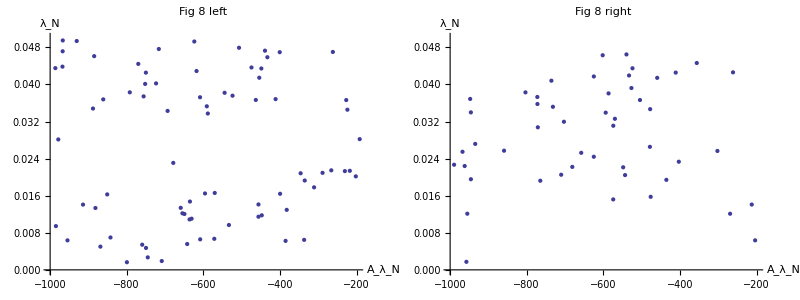

```mathematica
TableForm@{{p2D1,p2D2}}
```